# 1. Introduction

##### Paul Abbott paul.c.abbott@uwa.edu.au

## Recommended Reading

M L Boas, Mathematical Methods in the Physical Sciences, 3rd edition, Wiley, New York, 2006

J Mathews and R L Walker, Mathematical Methods of Physics, W. A. Benjamin, New York, 1970

MathWorld ⊳ mathworld.wolfram.com/

The Wolfram Functions Site ⊳ functions.wolfram.com/

L Shifrin, Mathematica Programming: an advanced introduction ⊳ www.mathprogramming-intro.org

## Course Overview

The tools you learn in this course are useful in all areas of mathematics, physics, and engineering.  Nearly all of the more advanced mathematical and physical concepts are built from this mathematics.

### This course has two aspects:

#### Mathematics

Vector spaces, matrices, and linear algebra

Calculus, ODEs and PDEs

Complex Algebra; Complex Functions

Fourier Series

Special functions

Variational methods and the action principle

Nonlinear systems

#### Mathematica

How Mathematica works

Basics of Mathematica programming

Dynamic functionality; use of Manipulate

Notebooks and Typesetting

Mathematica applied to the above areas of mathematics

## Introduction to Mathematica

### Videos and Online Tutorials

Wolfram Screencasts: http://www.wolfram.com/broadcast/screencasts

Mathematica Resources for Higher Education: http://www.wolfram.com/support/learn/higher-education.html

### Free-form input

-Graphics- (== at beginning of input) — use free-form linguistics to generate Mathematica output

(== == at beginning of input) — generate full Wolfram|Alpha output

-Graphics- (Ctrl+==) — enter free-form linguistics for conversion to inline Mathematica input

— open/close complete Wolfram|Alpha output

-Graphics- — Wolfram|Alpha result chosen for use in Mathematica

### The structure of Mathematica

As a computer application, Mathematica has two major components: the front end and the kernel.

#### Front end

The front end is what loads up when you start Mathematica. It allows you to load and manipulate notebooks and acts as interpreter between you and the kernel.

#### The kernel

The first expression you evaluate will start the kernel.

The kernel is where (nearly) all of your commands are processed. It is possible to use more than one kernel at a time, which can be located either locally or remotely.

### Getting Help

#### On-line Help

Under the Help Menu, there's many links to different aspects of Mathematica’s on-line documentation.

An overview of Mathematica is presented in the First Five Minutes with Mathematica section.

To get help on any specific function that is in a notebook, put the cursor over the function and press F1 (on a PC) or ⌘⇧[f] (on a Macintosh).

The on-line documentation has lots of examples, which are the best way to learn.

#### Palettes

When getting started with Mathematica the most useful palette under the Palettes menu is the Basic Math Assistant.

#### Command Completion and Templates

Long function names can be difficult to enter and remember; Complete Selection and Make Template under the Edit Menu increases the speed, correctness, and convenience of Notebooks.

Almost all commonly used front end commands have a shortcut key combination. They are listed next to the menu items in the menus.

### How the user sees everything

The user primarily works within a notebook. A notebook consists of a series of cells which are of the type, eg "Section", "Text", "Input", "Output", etc

If you move the mouse between two cells, the cursor will become horizontal. Clicking here and then typing will yield a new Input cell. Once entered (by pressing shift-return or enter) each input cell is assigned a number, and will return a corresponding output cell.

#### Examples: Mathematica as a calculator

Add 1+2:

```mathematica
1+2
```

Compute cos(3.14):

```mathematica
Cos[3.14]
```

-0.999999

Compute cos(3π):

```mathematica
cos(3π)
```

-1

#### StandardForm and TraditionalForm

The default form for human consumption is StandardForm. Like the Sin[Pi] expression above. Functions have Capitalised first letters and use square brackets, [] for their arguments.

TraditionalForm mimics traditional maths notation, using lower case letters and round parentheses. To save confusion we will normally use StandardForm.

To switch any expression between the above forms use the menu  Cell ▶ Convert To ▶ ⋯Form or the appropriate key combination. (PC keyboard shortcuts: Ctrl⇧[n] / Ctrl⇧[t])

### How the kernel sees everything

#### Expressions

Everything that Mathematica deals with is an Expression (the first principle of Mathematica). An expression is either Atomic or normal.

A normal expression consists of a Head and a list of arguments, eg  f[1,2,g[y,z],x]

Even Cells and Notebooks are expressions, e.g., Cell ▶ Show Expression or ⇧Ctrl[e]

Atomic expressions are elementary objects, such as a Number (2, 5.55, 1+2I), or a Symbol such as x:

```mathematica
{AtomQ[x],AtomQ[1],AtomQ[Sin[3]],AtomQ[Sin[π]]}
```

#### FullForm

Mathematica is most effective when treated as a  programming language (cf /).

When an input cell is entered it is translated into FullForm and passed to the kernel for evaluation:

```mathematica
FullForm[3(1+x^2)]
```

The nested structure of FullForm expressions can be displayed using TreeForm:

```mathematica
TreeForm[3(1+x^2)]
```

##### Aside

The form and behaviour of the Mathematica language can be compared with eg Lisp which is an implementation of Church's Lambda calculus.

In Lisp, the above expression would be written as (f,1,2,g[y,z],x).

The head of an expression is its 0^th part:

```mathematica
Part[f[1,2,g[y,z],x],0]
```

f

### Numbers

#### Exact numbers

Calculations involving only Integers, Rationals, Algebraics and expressions involving certain built in constants (eg, ⅇ, π, ℽ, ProtonMass, etc) are performed exactly.

To input Greek letters either use the palette or press, for example EscaEsc written as a to get α.

The base of the natural logarithm  E==ⅇ==ee  and I==ⅈ==ii

Compute sin(π/7):

```mathematica
Sin[π/7]
```

sin(π/7)

Compute the numerical value of sin(π/7):

```mathematica
N[%]
```

0.433884

The symbol % denotes the previous output. N[expr] gives the numerical value of expr.

Calculations can be performed with numbers of arbitrary size:

```mathematica
2^1000
```

10715086071862673209484250490600018105614048117055336074437503883703510511249361224931983788156958581275946729175531468251871452856923140435984577574698574803934567774824230985421074605062371141877954182153046474983581941267398767559165543946077062914571196477686542167660429831652624386837205668069376

#### Inexact numbers

Any expression with an inexact number (eg 3.14) is evaluated numerically:

```mathematica
Sin[3.14]
```

0.00159265

The Precision is tracked throughout the computation:

```mathematica
Precision[%]
```

MachinePrecision

If a decimal expression is entered with fewer than 16 decimal places, it is assumed to have MachinePrecision:

```mathematica
{N[MachinePrecision],N[Log[2,10]MachinePrecision]}
```

{15.9546,53.}

We can obtain the numerical value of any built-in constant to arbitrary precision:

```mathematica
N[π,2000]
```

3.1415926535897932384626433832795028841971693993751058209749445923078164062862089986280348253421170679821480865132823066470938446095505822317253594081284811174502841027019385211055596446229489549303819644288109756659334461284756482337867831652712019091456485669234603486104543266482133936072602491412737245870066063155881748815209209628292540917153643678925903600113305305488204665213841469519415116094330572703657595919530921861173819326117931051185480744623799627495673518857527248912279381830119491298336733624406566430860213949463952247371907021798609437027705392171762931767523846748184676694051320005681271452635608277857713427577896091736371787214684409012249534301465495853710507922796892589235420199561121290219608640344181598136297747713099605187072113499999983729780499510597317328160963185950244594553469083026425223082533446850352619311881710100031378387528865875332083814206171776691473035982534904287554687311595628638823537875937519577818577805321712268066130019278766111959092164201989380952572010654858632788659361533818279682303019520353018529689957736225994138912497217752834791315155748572424541506959508295331168617278558890750983817546374649393192550604009277016711390098488240128583616035637076601047101819429555961989467678374494482553797747268471040475346462080466842590694912933136770289891521047521620569660240580381501935112533824300355876402474964732639141992726042699227967823547816360093417216412199245863150302861829745557067498385054945885869269956909272107975093029553211653449872027559602364806654991198818347977535663698074265425278625518184175746728909777727938000816470600161452491921732172147723501414419735685481613611573525521334757418494684385233239073941433345477624168625189835694855620992192221842725502542568876717904946016534668049886272327917860857843838279679766814541009538837863609506800642251252051173929848960841284886269456042419652850222106611863067442786220391949450471237137869609563643719172874677646575739624138908658326459958133904780275901

#### Complex numbers

Compute 1+2ⅈ:

```mathematica
1+2 I
```

1+2 ⅈ

What is the FullForm of 1+2ⅈ?

```mathematica
FullForm[%]
```

Complex[1,2]

The different forms of the imaginary unit:

```mathematica
I==ⅈ==ⅉ==Complex[0,1]
```

True

The symbol == denotes the test Equal. It returns true if LHS==RHS and is distinct from = or Set which assigns the LHS to the value of the RHS.

#### Notation

Some notational issues.

ⅈ is not the letter i:

```mathematica
∑_(i=1)^4 ⅈ^i
```

0

ⅆ is not the letter d:

```mathematica
(ⅆ d^2)/ⅆd
```

2 d

```mathematica
∫d ⅆd
```

d^2/2

### Lists and operators

#### Lists, vectors, and matrices

A fundamental data type is the List, used for vectors and matrices—but can represent more complicated structures.

A vector:

```mathematica
{1,2,3}
```

{1,2,3}

```mathematica
%//FullForm
```

List[1,2,3]

A unit vector x̂:

```mathematica
x̂={1,0,0}
```

A 3×3 identity matrix:

```mathematica
id=IdentityMatrix[3];
```

#### Things you can do with lists

Dot product:

```mathematica
{1,2,3}.{1,2,3}
```

14

Cross product:

```mathematica
{1,2,3}×{1,2,5}
```

{4,-2,0}

Scalar multiplication:

```mathematica
{1,2,3}π
```

{π,2 π,3 π}

Apply Listable operations, such as power and functions, to a list:

```mathematica
{1,2,3}^2
```

{1,4,9}

```mathematica
Cos[{1,2,3}π]
```

{-1,1,-1}

Here is a matrix (list of lists):

```mathematica
{{a,b,c},{c,d,e}}
```

(a | b | c
c | d | e)

Here is the transpose of this matrix:

```mathematica
Transpose[%]
```

(a | c
b | d
c | e)

To compute the product of two matrices, use Dot product multiplication:

```mathematica
({{a, b, c}, {c, d, e}}).({{a, c}, {b, d}, {c, e}})
```

(a^2+b^2+c^2 | a c+e c+b d
a c+e c+b d | c^2+d^2+e^2)

#### Part (⟦ ⟧)

Part extracts part of any expression. Use Part[expr,i] or expr[[i]] or expr⟦i⟧  (where ⟦ is [[ )

The first part of a list:

```mathematica
Part[{a,b,c,d},1]
```

A 2×2 matrix 𝒜:

```mathematica
𝒜={{1,2},{3,4}}
```

𝒜_1.2:

```mathematica
𝒜[[1,2]]
```

The 3^rd part of a function:

```mathematica
f[x,y,z]⟦3⟧
```

#### Map (/@)

Map[f,expr] maps a function over an expression.

Two ways of mapping f over the list {w,x,y,z}:

```mathematica
Map[f,{w,x,y,z}]
```

```mathematica
f/@{w,x,y,z}
```

#### Apply (@@)

Apply applies a function to a list.

Apply f to {a,b,c}:

```mathematica
Apply[f,{a,b,c}]
```

```mathematica
f@@{a,b,c}
```

Apply f to g(a,b,c):

```mathematica
f@@g[a,b,c]
```

Apply replaces the Head of an expression:

```mathematica
Head[{a,b,c}]
```

#### ReplaceAll (/.)

ReplaceAll applies a set of replacement rules to all parts of an expression:

```mathematica
{1,2,3,4,3,2,1}/.{2->"two",4->"four"}
```

```mathematica
ReplaceAll[{1,2,3,4,3,2,1},{2->"two",4->"four"}]
```

#### Prefix, Postfix and Infix

A function/operator does not always have to be entered as f[⋯].

Prefix (good when you have functions of functions, reduces number of brackets):

```mathematica
f@g@x
```

Postfix (handy for things like //N,  //TraditionalForm,  //MatrixForm etc):

```mathematica
{1,2,Pi}//N
```

{1.,2.,3.14159}

Infix (common examples are +, -, ×, ·, ==, etc ):

```mathematica
x~f~y
```

##### Aside

Infix operations behave like +, -, …  for functions of more than two argument if they have the attribute Flat.

What are the Attributes of Plus?

```mathematica
Attributes[Plus]
```

Make f Flat:

```mathematica
SetAttributes[f,Flat]
```

```mathematica
x~f~y~f~z
```

### Some algebra

#### Polynomials

We can use any of these algebraic manipulations. Most useful are Expand, Factor, Collect, Simplify, FullSimplify, PowerExpand

Let's play with a quadratic. Note that the terms were put into a canonical order and the x terms combined, but that’s all:

```mathematica
x^2-3x-x  +4
```

x^2-4 x+4

If we want Mathematica to do any more, we have to ask:

```mathematica
Factor[%]
```

(x-2)^2

#### Trigonometry

Similarly with trigonometry, some simple replacements are made automatically but most have to be requested.

Change to polar coordinates:

```mathematica
x^2+y^2/.{x->r Cos[θ],y->r Sin[θ]}
```

r^2 sin^2(θ)+r^2 cos^2(θ)

Use TrigReduce:

```mathematica
TrigReduce@%
```

r^2

Use TrigExpand:

```mathematica
Cos[x+y+z]//TrigExpand
```

cos(x) cos(y) cos(z)-sin(x) sin(y) cos(z)-sin(x) cos(y) sin(z)-cos(x) sin(y) sin(z)

#### Solve

Solve a quadratic equation:

```mathematica
quadSoln=Solve[a x^2+b x+c==0,x]
```

{{x→(-√(b^2-4 a c)-b)/(2 a)},{x→(√(b^2-4 a c)-b)/(2 a)}}

Check the solution:

```mathematica
a x^2+b x+c==0/.quadSoln
```

{((-√(b^2-4 a c)-b)^2)/(4 a)+(b (-√(b^2-4 a c)-b))/(2 a)+c==0,((√(b^2-4 a c)-b)^2)/(4 a)+(b (√(b^2-4 a c)-b))/(2 a)+c==0}

```mathematica
%//Simplify
```

{True,True}

The solution to the general cubic a x^3+b x^2+c x+d==0 is complicated and not useful:

```mathematica
cubicSoln=Solve[a x^3+b x^2+c x+d==0,x]
```

{{x→((√((-27 a^2 d+9 a b c-2 b^3)^2+4 (3 a c-b^2)^3)-27 a^2 d+9 a b c-2 b^3)^(1/3))/(3 2^(1/3) a)-(2^(1/3) (3 a c-b^2))/(3 a (√((-27 a^2 d+9 a b c-2 b^3)^2+4 (3 a c-b^2)^3)-27 a^2 d+9 a b c-2 b^3)^(1/3))-b/(3 a)},{x→-((1-ⅈ √3) (√((-27 a^2 d+9 a b c-2 b^3)^2+4 (3 a c-b^2)^3)-27 a^2 d+9 a b c-2 b^3)^(1/3))/(6 2^(1/3) a)+((1+ⅈ √3) (3 a c-b^2))/(3 2^(2/3) a (√((-27 a^2 d+9 a b c-2 b^3)^2+4 (3 a c-b^2)^3)-27 a^2 d+9 a b c-2 b^3)^(1/3))-b/(3 a)},{x→-((1+ⅈ √3) (√((-27 a^2 d+9 a b c-2 b^3)^2+4 (3 a c-b^2)^3)-27 a^2 d+9 a b c-2 b^3)^(1/3))/(6 2^(1/3) a)+((1-ⅈ √3) (3 a c-b^2))/(3 2^(2/3) a (√((-27 a^2 d+9 a b c-2 b^3)^2+4 (3 a c-b^2)^3)-27 a^2 d+9 a b c-2 b^3)^(1/3))-b/(3 a)}}

Consider the roots of the quintic x^5- x+1==0:

```mathematica
roots=SolveValues[x^5- x+1==0,x]
```

{Root-1.17Root[1-#1+#1^5&,1]-1.1673039782614187,Root-0.181-1.08 ⅈRoot[1-#1+#1^5&,2]-0.18123244446987538,Root-0.181+1.08 ⅈRoot[1-#1+#1^5&,3]-0.18123244446987538,Root0.765-0.352 ⅈRoot[1-#1+#1^5&,4]0.7648844336005848,Root0.765+0.352 ⅈRoot[1-#1+#1^5&,5]0.7648844336005848}

Here are their numerical values:

```mathematica
N[roots,30]
```

{-1.16730397826141868425604589985,-0.18123244446987538390180023778-1.08395410131771066843034449298 ⅈ,-0.18123244446987538390180023778+1.08395410131771066843034449298 ⅈ,0.764884433600584726029823187709-0.3524715460317262493179470914 ⅈ,0.764884433600584726029823187709+0.3524715460317262493179470914 ⅈ}

What is the exact product of all the roots?

```mathematica
Apply[Times,roots]//Simplify
```

-1

### Some calculus

#### Derivative

Compute partial derivatives:

```mathematica
D[x^2,x]
```

2 x

```mathematica
D[Cos[x], x]
```

-Sin[x]

Compute the derivative of a Function:

```mathematica
Cos'
```

-Sin[#1]&

```mathematica
FullForm/@{f'[x],f''[x]}
```

{Derivative[1][f][x],Derivative[2][f][x]}

```mathematica
Derivative[1,2][f][x,y]
```

f^(1,2)(x,y)

Finally there are total derivatives:

```mathematica
Dt[f[x,y],x]
```

Dt[y,x] f^(0,1)[x,y]+f^(1,0)[x,y]

#### Integrals

An indefinite integral:

```mathematica
Integrate[x^n,x]
```

x^(n+1)/(n+1)

Check:

```mathematica
∂_x %
```

x^n

Understand what this means!

```mathematica
Derivative[-1][Function[x,x^n]][x]
```

x^(n+1)/(n+1)

Here is the same expression in TraditionalForm:

```mathematica
Derivative[-1][(x↦x^n)](x)
```

x^(n+1)/(n+1)

A definite integral:

```mathematica
Integrate[f[x],{x,a,b}]
```

∫_a^b f(x)ⅆx

Integrals can not always be done in closed form. In this case the integral is returned unevaluated. This usually means that no closed form is known in terms of  “standard” functions:

```mathematica
Integrate[x^x,{x,0,1}]
```

∫_0^1 x^x ⅆx

We can, of course, proceed numerically:

```mathematica
Integrate[x^x,{x,0,1}]//N
```

0.783431

```mathematica
NIntegrate[x^x,{x,0,1}]
```

0.783431

#### Sums

Compute ∑_(n=1)^∞ x_n:

```mathematica
Sum[Subscript[x, n],{n,1,∞}]
```

∑_(n=1)^∞ x_n

Compute ∑_(n=1)^∞ n^-2:

```mathematica
Sum[n^-2,{n,1,∞}]
```

π^2/6

Compute ∑_(n=1)^∞ n^-1:

```mathematica
Sum[n^-1,{n,1,∞}]
```

Sum::div: Sum does not converge.

∑_(n=1)^∞ 1/n

Compute ∑_(n=1)^∞ n^-s:

```mathematica
Sum[n^-s,{n,1,∞}]
```

s

### Graphics

Some simple examples follow. For more complete information about what's available, see here.

#### Two Dimensions

To make 2D plots use Plot:

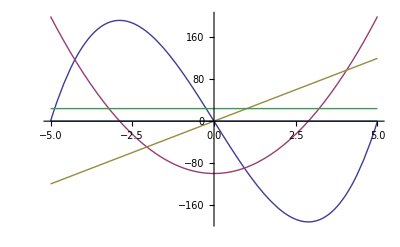

```mathematica
Plot[Evaluate@Table[D[4(x-5)x(x+5),{x,n}],{n,0,4}],{x,-5,5},PlotStyle->Thick]
```

#### Three Dimensions

To make 3D plots use Plot3D:

```mathematica
Plot3D[Sin[x y],{x,0,4},{y,0,4}]
```

-Graphics3D-

#### Sound

You can also Play functions:

```mathematica
Play[Sin[300t Sin[20t]],{t,-1,1}]
```

-Graphics-

```mathematica
Play[Sum[Sin[2000 2^t n t],{n,5}],{t,0,4}]
```

-Graphics-

### Defining functions and Pattern-matching

The final, essential bit of Mathematica we should cover before moving onto some real maths is how to define a function.

Without going into too much detail, here is an example:

```mathematica
h[x_]:=Sin[x^2]/x
```

We can then use this definition:

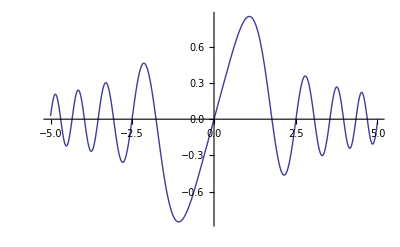

```mathematica
Plot[h[z],{z,-5,5},PlotRange->All]
```

```mathematica
h'[t]
```

2 cos(t^2)-(sin(t^2))/t^2

##### Notes

Note the syntax highlighting.

The underscore character is called a Blank. It means that the variable x is a dummy variable.

The  :=  is SetDelayed. This means that the right-hand side of the definition is not evaluated until the function is called.

### … and lots, lots more

These lectures were the Introduction to Mathematica. There is lots more that we'll learn as we go along!